## 1) TAS/MRC FUNCTIONS (Please, run sections 1-3 first)

### FUNCTION UPPER LIMIT OF SUMMARY OF THE MULTINOMIAL

```mathematica
Clear all;
LimiteSum::InconsistentCoeffs = "Inconsistent coefficients!";
LimiteSum[k_,m_] := Module[{},
Unprotect[Power];Power[0|0.,0|0.]=1;Protect[Power];(*Para revertir eso usar el siguiente codigo*)
(*Unprotect[Power];ClearAll[Power];Protect[Power];*)
combi=Table[PadRight[IntegerPartitions[k,m][[i]][[;;]],m],{i,1,Length[IntegerPartitions[k,m]]}];
permu=Table[Permutations[combi[[;;]][[i]]],{i,1,Length[combi]}];
permu=Flatten[permu];idx=1; Do[Subscript[per, idx]=Table[permu[[z]],{z,j,j+(m-1)}];idx++,{j,1,Length[permu],m}];
value=Length[permu]/m;
(*Returning back the value*)
Unprotect[Power];ClearAll[Power];Protect[Power];
Return[value];];
```

```mathematica
Clear all;
be1::InconsistentCoeffs = "Inconsistent coefficients!";
be1[i_,m_,μ_ ] := Module[{},
If[ 0≤ i≤ m-μ,value=i+1,value= m-μ+1] ;
Return[value];];
```

### FUNCTIONS OF COMBINATIONS FOR THE MULTINOMIAL

```mathematica
Clear all;
perm::InconsistentCoeffs = "Inconsistent coefficients!";
perm[k_,m_] := Module[{},
Unprotect[Power];Power[0|0.,0|0.]=1;Protect[Power];(*Para revertir eso usar el siguiente codigo*)
(*Unprotect[Power];ClearAll[Power];Protect[Power];*)
combi=Table[PadRight[IntegerPartitions[k,m][[i]][[;;]],m],{i,1,Length[IntegerPartitions[k,m]]}];
permu=Table[Permutations[combi[[;;]][[i]]],{i,1,Length[combi]}];
permu=Flatten[permu];idx=1; Do[Subscript[per, idx]=Table[permu[[z]],{z,j,j+(m-1)}];idx++,{j,1,Length[permu],m}];
combTotal=Table[Subscript[per, j],{j,1,Length[permu]/(m)}];
(*Returning back the value*)
Unprotect[Power];ClearAll[Power];Protect[Power];
Return[combTotal];];
```

### BETA FUNCTION FOR SIMPLE POWER SERIES

```mathematica
Clear all; (*este funciona bien para caso generico*)
beta::InconsistentCoeffs = "Inconsistent coefficients!";
beta[k_,n_,m_] := Module[{},
Subscript[beta, 0,0]=1;
Subscript[beta, 1,n]=n; 
Subscript[beta, 0,n]=1; 
If[n==1,Subscript[beta, k,1]=1/(k!)]  ;                
If[n≥ 1,Subscript[beta, k,n]=∑_(j=k-( m-1))^k If[0≤ j≤ (n-1)(m-1),Subscript[beta, j,n-1]/((k-j)!) ,0]]  ;                        
(*Returning back the value*)
Return[Subscript[beta, k,n]];];
```

## 2 ) ASC and Asymptotic expressions for (m < μ) Eq. (30) and Eq. (33)

### Definitions

```mathematica
A1[j_,μ_,κ_,m_]:=(-1)^m Binomial[m+j-2,j-1](m/(μ κ+m))^m((μ κ)/(μ κ+m))^(-m-j+1)
A2[j_,μ_,κ_,m_]:=(-1)^(j-1)Binomial[μ-m+j-2,j-1](m/(μ κ+m))^(j-1)((μ κ)/(μ κ+m))^(m-μ-j+1)
Delta1[μ_,κ_,γMed_]:=γMed/(μ (1+κ))
B[j_,μ_,κ_,m_]:=Binomial[m-μ,j](m/(μ κ+m))^j((μ κ)/(μ κ+m))^(m-μ-j) 
Delta2[μ_,κ_,γMed_,m_]:=(μ κ+m)/m γMed/(μ (1+κ)) 
wB[j_,μ_,κ_,γMed_,m_]:=Delta2[μ,κ,γMed,m](m-j)
wA1[j_,m_,μ_,κ_,γMed_]:=Delta1[μ,κ,γMed](μ-m-j+1)
wA2[j_,m_,μ_,κ_,γMed_]:=Delta2[μ,κ,γMed,m](m-j+1)
```

### Asymptotic ASC at Bob

```mathematica
CsAsintv1[μb_,κb_,mb_,γMedb_,NA_,NB_]:=Log2[ NB γMedb]+Log2[ⅇ](∑_(h=1)^NA (-1)^h Binomial[NA,h] ∑_(k=0)^h Binomial[h,k]∑_(i3=1)^LimiteSum[k,mb NB] ((k)!)/(∏_(u3=1)^(mb NB) perm[k,mb NB][[i3]][[u3]]!)(∏_(t2=1)^(mb NB) (((NB γMedb)/Delta2[μb NB,κb,γMedb NB,mb NB])^(NB mb-t2)1/((mb NB-t2)!) ∑_(z=mb NB+1-t2)^(mb NB) A2[mb NB+1-z,μb NB,κb,mb NB])^(perm[k,mb NB][[i3]][[t2]]))   ∑_(i2=1)^LimiteSum[h-k,μb NB-mb NB] ((h-k)!)/(∏_(u=1)^(μb NB-mb NB) perm[h-k,μb NB-mb NB][[i2]][[u]]!)(∏_(t=1)^(μb NB-mb NB) (((NB  γMedb)/Delta1[μb NB,κb,γMedb NB] )^(μb NB-mb NB-t)1/((μb NB-mb NB-t)!) ∑_(z=μb NB-mb NB+1-t)^(μb NB-mb NB) A1[μb NB-mb NB+1-z,μb NB,κb,mb NB])^(perm[h-k,μb NB-mb NB][[i2]][[t]]))If[∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]]==0,EulerGamma+Log[ ((h-k)  γMedb NB)/Delta1[μb NB,κb,γMedb NB]+ (k γMedb NB)/Delta2[μb NB,κb,γMedb NB,mb NB]],  -((γMedb NB (k Delta1[μb NB,κb,γMedb NB]+Delta2[μb NB,κb,γMedb NB,mb NB]  (h-k)))/(Delta2[μb NB,κb,γMedb NB,mb NB]  Delta1[μb NB,κb,γMedb NB]) )^(-(∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]])) Gamma[     ∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+  ∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]]]] )
```

#### ASC at Eve

```mathematica
CeV1[μe_,κe_,me_,γMede_,NE_]:=1/Log[2]( Exp[1/Delta1[μe NE,κe,γMede NE]] ∑_(j=1)^(μe NE-me NE) A1[j,μe NE,κe,me NE] ∑_(r=0)^(μe NE-me NE-j) 1/(r!)(1/Delta1[μe NE,κe,γMede NE])^r Gamma[1+r] Gamma[-r,1/Delta1[μe NE,κe,γMede NE]] +Exp[ 1/Delta2[μe NE,κe,γMede NE,me NE]]∑_(j=1)^(me NE) A2[j,μe NE,κe,me NE] ∑_(r=0)^(me NE-j) 1/(r!)(1/Delta2[μe NE,κe,γMede NE,me NE])^r   Gamma[1+r]Gamma[-r,1/Delta2[μe NE,κe,γMede NE,me NE]])
```

#### Asymptotic ASC Eq. (33) of paper

```mathematica
ascV1Asintotico[μb_,μe_,κb_,κe_,mb_,me_,γMedb_,γMede_,NA_,NB_,NE_]:=CsAsintv1[μb,κb,mb,γMedb,NA,NB]-CeV1[μe,κe,me,γMede,NE]
```

### Proposed ASC closed form solution for Bob

#### ASC Loss

```mathematica
ascLossV1[μb_,μe_,κb_,κe_,mb_,me_,γMedb_,γMede_,NA_,NB_,NE_]:=1/Log[2]∑_(h=1)^NA (-1)^(h+1)Binomial[NA,h] ∑_(k=0)^h Binomial[h,k]∑_(i3=1)^LimiteSum[k,mb NB] ((k)!)/(∏_(u3=1)^(mb NB) perm[k,mb NB][[i3]][[u3]]!)(∏_(t2=1)^(mb NB) ((1/Delta2[μb NB,κb,γMedb NB,mb NB])^(mb NB-t2)1/((mb NB-t2)!) ∑_(z=mb NB+1-t2)^(mb NB) A2[mb NB+1-z,μb NB,κb,mb NB])^(perm[k,mb NB][[i3]][[t2]]))∑_(i2=1)^LimiteSum[h-k,μb NB-mb NB] ((h-k)!)/(∏_(u=1)^(μb NB-mb NB) perm[h-k,μb NB-mb NB][[i2]][[u]]!)(∏_(t=1)^(μb NB-mb NB) ((1/Delta1[μb NB,κb,γMedb NB])^(μb NB-mb NB-t)1/((μb NB-mb NB-t)!) ∑_(z=μb NB-mb NB+1-t)^(μb NB-mb NB) A1[μb NB-mb NB+1-z,μb NB,κb,mb NB])^(perm[h-k,μb NB-mb NB][[i2]][[t]]))Exp[(h-k)/Delta1[μb NB,κb,γMedb NB]+k/Delta2[μb NB,κb,γMedb NB,mb NB]](∑_(j=1)^(μe NE-me NE) A1[j,μe NE,κe,me NE] ∑_(r=0)^(μe NE-me NE-j) 1/(r!)(1/Delta1[μe NE,κe,γMede NE])^r  Exp[1/Delta1[μe NE,κe,γMede NE]]Gamma[1+r+∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]]]Gamma[-r-∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]-∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]],(h-k)/Delta1[μb NB,κb,γMedb NB]+k/Delta2[μb NB,κb,γMedb NB,mb NB]+1/Delta1[μe NE,κe,γMede NE]]+∑_(j=1)^(me NE) A2[j,μe NE,κe ,me NE] ∑_(r=0)^(me NE-j) 1/(r!)(1/Delta2[μe NE,κe,γMede NE,me NE])^r   Exp[1/Delta2[μe NE,κe,γMede NE,me NE]]Gamma[1+r+∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]]]Gamma[-r-∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]-∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]],(h-k)/Delta1[μb NB,κb,γMedb NB]+k/Delta2[μb NB,κb,γMedb NB,mb NB]+1/Delta2[μe NE,κe,γMede NE,me NE]])
```

#### Exact ASC at Bob

```mathematica
CbobV1[μb_,κb_,mb_,γMedb_,NA_,NB_]:=1/Log[2]∑_(h=1)^NA (-1)^(h+1)Binomial[NA,h] ∑_(k=0)^h Binomial[h,k]∑_(i3=1)^LimiteSum[k,mb NB] ((k)!)/(∏_(u3=1)^(mb NB) perm[k,mb NB][[i3]][[u3]]!)(∏_(t2=1)^(mb NB) ((1/Delta2[μb NB,κb ,γMedb NB,mb NB])^(mb NB-t2)1/((mb NB-t2)!) ∑_(z=mb NB+1-t2)^(mb NB) A2[mb NB+1-z,μb NB,κb,mb NB])^(perm[k,mb NB][[i3]][[t2]]))∑_(i2=1)^LimiteSum[h-k,μb NB-mb NB] ((h-k)!)/(∏_(u=1)^(μb NB-mb NB) perm[h-k,μb NB-mb NB][[i2]][[u]]!)(∏_(t=1)^(μb NB-mb NB) ((1/Delta1[μb NB,κb,γMedb NB])^(μb NB-mb NB-t)1/((μb NB-mb NB-t)!) ∑_(z=μb NB-mb NB+1-t)^(μb NB-mb NB) A1[μb NB-mb NB+1-z,μb NB,κb,mb NB])^(perm[h-k,μb NB-mb NB][[i2]][[t]]))  Exp[(h-k)/Delta1[μb NB,κb,γMedb NB]+k/Delta2[μb NB,κb,γMedb NB,mb NB]] Gamma[1+∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB- mb NB][[i2]][[t]]] Gamma[-∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]-∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]],(h-k)/Delta1[μb NB,κb,γMedb NB]+k/Delta2[μb NB,κb,γMedb NB,mb NB]]
```

#### Proposed ASC Eq. (30)

```mathematica
ascV1Total[μb_,μe_,κb_,κe_,mb_,me_,γMedb_,γMede_,NA_,NB_,NE_]:=CbobV1[μb,κb,mb,γMedb,NA,NB]-(ascLossV1[μb,μe,κb,κe,mb,me,γMedb,γMede,NA,NB,NE])
```

## 3) ASC and Asymptotic expressions for (m >= μ) Eq. (29) and Eq. (34)

### Definitions

```mathematica
A1[j_,μ_,κ_,m_]:=(-1)^m Binomial[m+j-2,j-1](m/(μ κ+m))^m((μ κ)/(μ κ+m))^(-m-j+1)
A2[j_,μ_,κ_,m_]:=(-1)^(j-1)Binomial[μ-m+j-2,j-1](m/(μ κ+m))^(j-1)((μ κ)/(μ κ+m))^(m-μ-j+1)
Delta1[μ_,κ_,γMed_]:=γMed/(μ (1+κ))
B[j_,μ_,κ_,m_]:=Binomial[m-μ,j](m/(μ κ+m))^j((μ κ)/(μ κ+m))^(m-μ-j) 
Delta2[μ_,κ_,γMed_,m_]:=(μ κ+m)/m γMed/(μ (1+κ)) 
wB[j_,μ_,κ_,γMed_,m_]:=Delta2[μ,κ,γMed,m](m-j)
```

### Asymptotic ASC at Bob

```mathematica
CsAsintv2[μ_,κ_,m_,γMed_,NA_,NB_]:=Log2[ NB γMed]+Log2[ⅇ]∑_(h=1)^NA (-1)^h Binomial[NA,h]∑_(i2=1)^LimiteSum[h,m NB] (h!)/(∏_(u=1)^(m NB) perm[h,m NB][[i2]][[u]]!)(∏_(t=1)^(m NB) (((NB  γMed)/Delta2[μ NB,κ,γMed NB,m NB])^(m NB-t)1/((m NB-t)!) ∑_(z=m NB-μ NB+1-be1[t-1,m NB,μ NB])^(m NB-μ NB) B[m NB-μ NB-z,μ NB,κ ,m NB]  )^(perm[h,m NB][[i2]][[t]]))If[∑_(t=1)^(m NB) (m NB-t)perm[h,m NB][[i2]][[t]]==0,EulerGamma+Log[(h  NB  γMed)/Delta2[μ NB,κ,γMed NB,m NB]],-((h NB  γMed)/Delta2[μ NB,κ,γMed NB,m NB])^(-(∑_(t=1)^(m NB) (m NB -t)perm[h,m NB ][[i2]][[t]])) Gamma[∑_(t=1)^(m NB) (m NB -t)perm[h,m NB ][[i2]][[t]]]]
```

#### ASC at Eve

```mathematica
CeV2[μe_,κe_,me_,γMede_,NE_]:=1/Log[2] Exp[ 1/Delta2[NE  μe,κe,NE γMede,NE me]]∑_(j=0)^(NE me-NE μe) B[j,NE μe, κe,NE me] ∑_(r=0)^(NE me-j-1) 1/(r!)(1/Delta2[NE μe,κe,NE γMede,NE me])^r Gamma[1+r]Gamma[-r,1/Delta2[NE μe,κe,NE γMede,NE me]]
```

#### Proposed Asymptotic ASC Eq. (34)

```mathematica
ascV2Asintotico[μb_,μe_,κb_,κe_,mb_,me_,γMedb_,γMede_,NA_,NB_,NE_]:=CsAsintv2[μb,κb,mb,γMedb,NA,NB]-CeV2[μe,κe,me,γMede,NE]
```

### Proposed Closed form solution for ASC

#### ASC LOSS

```mathematica
ascLossV2[μb_,μe_,κb_,κe_,mb_,me_,γMedb_,γMede_,NA_,NB_,NE_]:=1/Log[2]∑_(h=1)^NA (-1)^(h+1)Binomial[NA,h]∑_(i2=1)^LimiteSum[h,NB mb] (h!)/(∏_(u=1)^(NB mb) perm[h,NB mb][[i2]][[u]]!)(∏_(t=1)^(NB mb) ((1/Delta2[NB μb,κb,NB γMedb,NB mb])^(NB mb-t)1/((NB mb-t)!) ∑_(z=NB mb-μb NB+1-be1[t-1,NB mb,NB μb])^(NB mb-NB μb) B[NB mb-NB μb-z,NB μb,NB κb,NB mb]  )^(perm[h,NB mb][[i2]][[t]])) ∑_(j=0)^(NE me-NE μe) B[j,μe NE,κe,NE me]∑_(r=0)^(NE me-j-1) 1/(r!)(1/Delta2[μe NE,κe,NE γMede,NE me])^r  Exp[h/Delta2[NB μb,κb,NB γMedb,NB  mb]+1/Delta2[NE μe,κe,NE γMede,NE me]]     Gamma[1+r+∑_(t=1)^(NB mb) (NB mb-t)perm[h,NB mb][[i2]][[t]]] Gamma[-r-∑_(t=1)^(NB mb) (NB mb-t)perm[h,NB mb][[i2]][[t]],h/Delta2[NB μb,κb,NB γMedb,NB mb]+1/Delta2[ NE μe, κe,NE γMede,NE me]]
```

#### Exact ASC at Bob

```mathematica
CbobV2[μb_,κb_,mb_,γMedb_,NA_,NB_]:=1/Log[2]∑_(h=1)^NA (-1)^(h+1)Binomial[NA,h]∑_(i2=1)^LimiteSum[h,NB mb] (h!)/(∏_(u=1)^(NB mb) perm[h,NB mb][[i2]][[u]]!)(∏_(t=1)^(NB mb) ((1/Delta2[NB μb,κb,NB γMedb,NB mb])^(NB mb-t)1/((NB mb-t)!) ∑_(z=NB mb-μb NB+1-be1[t-1,NB mb,NB μb])^(NB mb-NB μb) B[NB mb-NB μb-z,NB μb,κb,NB mb]  )^(perm[h,NB mb][[i2]][[t]]))Exp[ h/Delta2[NB μb,κb,NB γMedb,NB mb]] Gamma[1+∑_(t=1)^(NB mb) (NB mb-t)perm[h,NB mb][[i2]][[t]]] Gamma[-∑_(t=1)^(NB mb) (NB mb-t)perm[h,NB mb][[i2]][[t]],h/Delta2[NB μb,κb,NB γMedb,NB mb]]
```

#### Proposed ASC Eq. (29)

```mathematica
ascV2Total[μb_,μe_,κb_,κe_,mb_,me_,γMedb_,γMede_,NA_,NB_,NE_]:=CbobV2[μb,κb,mb,γMedb,NA,NB]-(ascLossV2[μb,μe,κb,κe,mb,me,γMedb,γMede,NA,NB,NE])
```

## Figure 8 (by varying the numbers of antennas at NA-transmitter, NB-legitimate receiver and NE-eavesdropper receiver )

### For m=1,μ=2, NE=2, NB=2, κ = 5, and NA=2 (Case 1-Fig.8)

#### Proposed Approach

```mathematica
μb=2;κb=5;mb=1;μe=2;κe=5;me=1;NA=2;NB=2; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase1Fig8= Table[{r,ascV1Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{1.24323,{{0.,0.021386},{2.,0.0664055},{4.,0.173731},{6.,0.385505},{8.,0.732815},{10.,1.21283},{12.,1.78905},{14.,2.41692},{16.,3.06623},{18.,3.72333},{20.,4.38355},{22.,5.04536},{24.,5.70813},{26.,6.37149}}}

```mathematica
Export["ascApproachCase1Fig8.mat",ascApproachCase1Fig8] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic approach

```mathematica
AbsoluteTiming[ascApproachCase1Fig8Asymp= Table[{r,ascV1Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{0.330707,{{0.,-2.26727},{3.,-1.27069},{6.,-0.274113},{9.,0.722465},{12.,1.71904},{15.,2.71562},{18.,3.7122},{21.,4.70878},{24.,5.70536},{27.,6.70194}}}

```mathematica
Export["ascApproachCase1Fig8Asymp.mat",ascApproachCase1Fig8Asymp] ;  (*Export the data to plot in MATLAB*)
```

### For m=1,μ=2, NE=2, NB=5, κ = 5, and NA=2 (Case 2-Fig.8)

#### Proposed Approach

```mathematica
μb=2;κb=5;mb=1;μe=2;κe=5;me=1;NA=2;NB=5; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase2Fig8= Table[{r,ascV1Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{19.3917,{{0.,0.130597},{2.,0.319614},{4.,0.655814},{6.,1.14338},{8.,1.73588},{10.,2.37523},{12.,3.02895},{14.,3.68724},{16.,4.34781},{18.,5.00978},{20.,5.67264},{22.,6.33607},{24.,6.99984},{26.,7.66385}}}

```mathematica
Export["ascApproachCase2Fig8.mat",ascApproachCase2Fig8] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic Approach

```mathematica
AbsoluteTiming[ascApproachCase2Fig8Asymp= Table[{r,ascV1Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{5.11385,{{0.,-0.973823},{3.,0.0227554},{6.,1.01933},{9.,2.01591},{12.,3.01249},{15.,4.00907},{18.,5.00565},{21.,6.00223},{24.,6.9988},{27.,7.99538}}}

```mathematica
Export["ascApproachCase2Fig8Asymp.mat",ascApproachCase2Fig8Asymp] ;  (*Export the data to plot in MATLAB*)
```

### For m=1,μ=2, NE=2, NB=2, κ = 5, and NA=5 (Case 3-Fig.8)

#### Proposed Approach

```mathematica
μb=2;κb=5;mb=1;μe=2;κe=5;me=1;NA=5;NB=2; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase3Fig8= Table[{r,ascV1Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{12.2534,{{0.,0.0404883},{2.,0.118986},{4.,0.292411},{6.,0.605344},{8.,1.06873},{10.,1.64498},{12.,2.27755},{14.,2.92934},{16.,3.58699},{18.,4.24722},{20.,4.90898},{22.,5.5717},{24.,6.23504},{26.,6.89876}}}

```mathematica
Export["ascApproachCase3Fig8.mat",ascApproachCase3Fig8] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic Approach

```mathematica
AbsoluteTiming[ascApproachCase3Fig8Asymp= Table[{r,ascV1Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{1.87605,{{0.,-1.73938},{3.,-0.742805},{6.,0.253774},{9.,1.25035},{12.,2.24693},{15.,3.24351},{18.,4.24009},{21.,5.23667},{24.,6.23324},{27.,7.22982}}}

```mathematica
Export["ascApproachCase3Fig8Asymp.mat",ascApproachCase3Fig8Asymp] ;  (*Export the data to plot in MATLAB*)
```

### For m=1,μ=2, NE=5, NB=2, κ = 5, and NA=2 (Case 4-Fig.8)

#### Proposed approach

```mathematica
μb=2;κb=5;mb=1;μe=2;κe=5;me=1;NA=2;NB=2; NE=5;
```

```mathematica
AbsoluteTiming[ascApproachCase4Fig8= Table[{r,ascV1Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{4.19705,{{0.,0.0000164459},{2.,0.000241632},{4.,0.00240422},{6.,0.0162424},{8.,0.0752186},{10.,0.244465},{12.,0.582623},{14.,1.08387},{16.,1.68655},{18.,2.33165},{20.,2.98968},{22.,3.65121},{24.,4.31395},{26.,4.97731}}}

```mathematica
Export["ascApproachCase4Fig8.mat",ascApproachCase4Fig8] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic Approach

```mathematica
AbsoluteTiming[ascApproachCase4Fig8Asymp= Table[{r,ascV1Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{0.378548,{{0.,-3.66145},{3.,-2.66487},{6.,-1.66829},{9.,-0.671716},{12.,0.324862},{15.,1.32144},{18.,2.31802},{21.,3.3146},{24.,4.31118},{27.,5.30775}}}

```mathematica
Export["ascApproachCase4Fig8Asymp.mat",ascApproachCase4Fig8Asymp] ;  (*Export the data to plot in MATLAB*)
```

#### PLOTS (Verification)

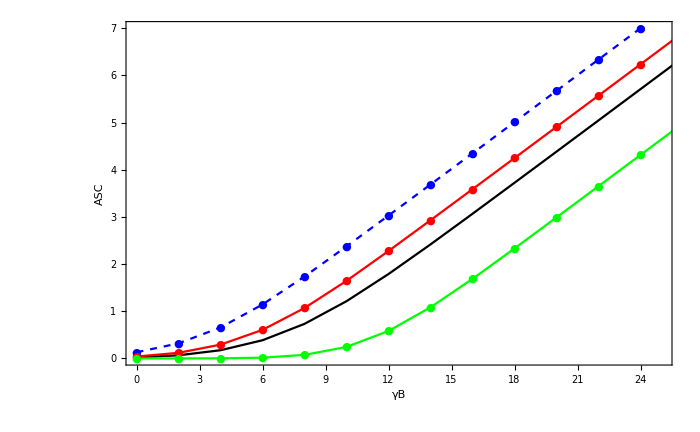

```mathematica
ListPlot[{ascApproachCase1Fig8,ascApproachCase2Fig8,ascApproachCase3Fig8,ascApproachCase4Fig8},PlotRange->{{0,25},{0,7}},Joined->{True,True,True},PlotStyle->{Directive[Black],Directive[Blue,Dashed],Directive[Red],Directive[Green]},FrameLabel->{Text[Style["γB",20]],Text[Style["ASC",20]]},LabelStyle->Directive[Black,FontSize->18],PlotMarkers-> {"","●","●","●"},PlotLegends->Placed[LineLegend[{},Joined->Automatic,LegendMarkers->Automatic,LegendFunction->"Frame",LegendMargins->{{8,8},{0.5,0.5}},LabelStyle->{FontFamily->"Times",FontSize->12}],{Left,Top}],Frame->True,AxesOrigin->{-35,0},ImageSize->700]
```

## Figure 9 (by varying the number of antennas at the legitimate receiver Bob-NB)

### For m=μ, NA=2, NE=2, NB=1, κ = 1.5 (Case 1-Fig 9)

#### Proposed Approach

```mathematica
μb=2;κb=1.5;mb=2;μe=2;κe=1.5;me=2;NA=2;NB=1; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase1Fig9= Table[{r,ascV2Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{0.176237,{{0.,0.000784738},{2.,0.00409517},{4.,0.0180673},{6.,0.0655202},{8.,0.191343},{10.,0.44838},{12.,0.858709},{14.,1.39386},{16.,2.00196},{18.,2.64278},{20.,3.29631},{22.,3.95488},{24.,4.61583},{26.,5.27809}}}

```mathematica
Export["ascApproachCase1Fig9.mat",ascApproachCase1Fig9] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic Approach

```mathematica
AbsoluteTiming[ascApproachCase1Fig9Asymp= Table[{r,ascV2Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{0.0409866,{{0.,-3.36255},{3.,-2.36597},{6.,-1.36939},{9.,-0.372812},{12.,0.623766},{15.,1.62034},{18.,2.61692},{21.,3.6135},{24.,4.61008},{27.,5.60666}}}

```mathematica
Export["ascApproachCase1Fig9Asymp.mat",ascApproachCase1Fig9Asymp] ;  (*Export the data to plot in MATLAB*)
```

### For m=μ, NA=2, NE=2, NB=1, κ = 10 (Case 2-Fig 9)

#### Proposed Approach

```mathematica
μb=2;κb=10.;mb=2;μe=2;κe=10.;me=2;NA=2;NB=1; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase2Fig9= Table[{r,ascV2Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{0.220565,{{0.,0.000784738},{2.,0.00409517},{4.,0.0180673},{6.,0.0655202},{8.,0.191343},{10.,0.44838},{12.,0.858709},{14.,1.39386},{16.,2.00196},{18.,2.64278},{20.,3.29631},{22.,3.95488},{24.,4.61583},{26.,5.27809}}}

```mathematica
Export["ascApproachCase2Fig9.mat",ascApproachCase2Fig9] ;  (*Export the data to plot in MATLAB*)
```

#### Asymptotic Proposed Approach

```mathematica
AbsoluteTiming[ascApproachCase2Fig9Asymp= Table[{r,ascV2Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{0.038434,{{0.,-3.36255},{3.,-2.36597},{6.,-1.36939},{9.,-0.372812},{12.,0.623766},{15.,1.62034},{18.,2.61692},{21.,3.6135},{24.,4.61008},{27.,5.60666}}}

```mathematica
Export["ascApproachCase2Fig9Asymp.mat",ascApproachCase2Fig9Asymp] ;  (*Export the data to plot in MATLAB*)
```

### For m=μ, NA=2, NE=2, NB=2, κ = 1.5 (Case 3-Fig 9)

#### Proposed Approach

```mathematica
μb=2;κb=1.5;mb=2;μe=2;κe=1.5;me=2;NA=2;NB=2; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase3Fig9= Table[{r,ascV2Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{1.33911,{{0.,0.00468214},{2.,0.0215894},{4.,0.0813955},{6.,0.243365},{8.,0.569923},{10.,1.06491},{12.,1.66533},{14.,2.30704},{16.,2.96096},{18.,3.61921},{20.,4.27976},{22.,4.94171},{24.,5.60456},{26.,6.26798}}}

```mathematica
Export["ascApproachCase3Fig9.mat",ascApproachCase3Fig9] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic Approach

```mathematica
AbsoluteTiming[ascApproachCase3Fig9Asymp= Table[{r,ascV2Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{0.448662,{{0.,-2.37069},{3.,-1.37412},{6.,-0.377538},{9.,0.61904},{12.,1.61562},{15.,2.6122},{18.,3.60878},{21.,4.60535},{24.,5.60193},{27.,6.59851}}}

```mathematica
Export["ascApproachCase3Fig9Asymp.mat",ascApproachCase3Fig9Asymp] ;  (*Export the data to plot in MATLAB*)
```

### For m=μ, NA=2, NE=2, NB=2, κ = 10 (Case 4-Fig 9)

#### Proposed Approach

```mathematica
μb=2;κb=10.;mb=2;μe=2;κe=10.;me=2;NA=2;NB=2; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase4Fig9= Table[{r,ascV2Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{1.39009,{{0.,0.00468214},{2.,0.0215894},{4.,0.0813955},{6.,0.243365},{8.,0.569923},{10.,1.06491},{12.,1.66533},{14.,2.30704},{16.,2.96096},{18.,3.61921},{20.,4.27976},{22.,4.94171},{24.,5.60456},{26.,6.26798}}}

```mathematica
Export["ascApproachCase4Fig9.mat",ascApproachCase4Fig9] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic Approach

```mathematica
AbsoluteTiming[ascApproachCase4Fig9Asymp= Table[{r,ascV2Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{0.262274,{{0.,-2.37069},{3.,-1.37412},{6.,-0.377538},{9.,0.61904},{12.,1.61562},{15.,2.6122},{18.,3.60878},{21.,4.60535},{24.,5.60193},{27.,6.59851}}}

```mathematica
Export["ascApproachCase4Fig9Asymp.mat",ascApproachCase4Fig9Asymp] ;  (*Export the data to plot in MATLAB*)
```

### For m=μ, NA=2, NE=2, NB=3, κ = 1.5 (Case 5-Fig 9)

#### Proposed Approach

```mathematica
μb=2;κb=1.5;mb=2;μe=2;κe=1.5;me=2;NA=2;NB=3; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase5Fig9= Table[{r,ascV2Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{5.90784,{{0.,0.0140735},{2.,0.0581174},{4.,0.190954},{6.,0.486428},{8.,0.966014},{10.,1.56499},{12.,2.20766},{14.,2.86163},{16.,3.51967},{18.,4.18005},{20.,4.8419},{22.,5.50469},{24.,6.16806},{26.,6.83181}}}

```mathematica
Export["ascApproachCase5Fig9.mat",ascApproachCase5Fig9] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic Approach

```mathematica
AbsoluteTiming[ascApproachCase5Fig9Asymp= Table[{r,ascV2Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{2.15168,{{0.,-1.8063},{3.,-0.809718},{6.,0.18686},{9.,1.18344},{12.,2.18002},{15.,3.1766},{18.,4.17317},{21.,5.16975},{24.,6.16633},{27.,7.16291}}}

```mathematica
Export["ascApproachCase5Fig9Asymp.mat",ascApproachCase5Fig9Asymp] ;  (*Export the data to plot in MATLAB*)
```

### For m=μ, NA=2, NE=2, NB=3, κ = 10 (Case 6-Fig 9)

#### Proposed Approach

```mathematica
μb=2;κb=10.;mb=2;μe=2;κe=10.;me=2;NA=2;NB=3; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase6Fig9= Table[{r,ascV2Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{6.22131,{{0.,0.0140735},{2.,0.0581174},{4.,0.190954},{6.,0.486428},{8.,0.966014},{10.,1.56499},{12.,2.20766},{14.,2.86163},{16.,3.51967},{18.,4.18005},{20.,4.8419},{22.,5.50469},{24.,6.16806},{26.,6.83181}}}

```mathematica
Export["ascApproachCase6Fig9.mat",ascApproachCase6Fig9] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic Approach

```mathematica
AbsoluteTiming[ascApproachCase6Fig9Asymp= Table[{r,ascV2Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{1.55699,{{0.,-1.8063},{3.,-0.809718},{6.,0.18686},{9.,1.18344},{12.,2.18002},{15.,3.1766},{18.,4.17317},{21.,5.16975},{24.,6.16633},{27.,7.16291}}}

```mathematica
Export["ascApproachCase6Fig9Asymp.mat",ascApproachCase6Fig9Asymp] ;  (*Export the data to plot in MATLAB*)
```

### For m=μ, NA=2, NE=2, NB=4, κ = 1.5 (Case 7-Fig 9)

#### Proposed Approach

```mathematica
μb=2;κb=1.5;mb=2;μe=2;κe=1.5;me=2;NA=2;NB=4; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase7Fig9= Table[{r,ascV2Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{22.5699,{{0.,0.0306062},{2.,0.11439},{4.,0.333106},{6.,0.744273},{8.,1.31176},{10.,1.9465},{12.,2.59829},{14.,3.25515},{16.,3.91479},{18.,4.57617},{20.,5.23866},{22.,5.90184},{24.,6.56547},{26.,7.22938}}}

```mathematica
Export["ascApproachCase7Fig9.mat",ascApproachCase7Fig9] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic Approach

```mathematica
AbsoluteTiming[ascApproachCase7Fig9Asymp= Table[{r,ascV2Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{5.42654,{{0.,-1.40846},{3.,-0.411877},{6.,0.584701},{9.,1.58128},{12.,2.57786},{15.,3.57444},{18.,4.57102},{21.,5.56759},{24.,6.56417},{27.,7.56075}}}

```mathematica
Export["ascApproachCase7Fig9Asymp.mat",ascApproachCase7Fig9Asymp] ;  (*Export the data to plot in MATLAB*)
```

### For m=μ, NA=2, NE=2, NB=4, κ = 10 (Case 7-Fig 9)

#### Proposed Approach

```mathematica
μb=2;κb=10.;mb=2;μe=2;κe=10.;me=2;NA=2;NB=4; NE=2;
```

```mathematica
AbsoluteTiming[ascApproachCase8Fig9= Table[{r,ascV2Total[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,26,2}]//N]
```

{22.3151,{{0.,0.0306062},{2.,0.11439},{4.,0.333106},{6.,0.744273},{8.,1.31176},{10.,1.9465},{12.,2.59829},{14.,3.25515},{16.,3.91479},{18.,4.57617},{20.,5.23866},{22.,5.90184},{24.,6.56547},{26.,7.22938}}}

```mathematica
Export["ascApproachCase8Fig9.mat",ascApproachCase8Fig9] ;  (*Export the data to plot in MATLAB*)
```

#### Proposed Asymptotic Approach

```mathematica
AbsoluteTiming[ascApproachCase8Fig9Asymp= Table[{r,ascV2Asintotico[μb,μe,κb,κe,mb,me,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,27,3}]//N]
```

{5.73634,{{0.,-1.40846},{3.,-0.411877},{6.,0.584701},{9.,1.58128},{12.,2.57786},{15.,3.57444},{18.,4.57102},{21.,5.56759},{24.,6.56417},{27.,7.56075}}}

```mathematica
Export["ascApproachCase8Fig9Asymp.mat",ascApproachCase8Fig9Asymp] ;  (*Export the data to plot in MATLAB*)
```

#### PLOTS (Verification)

```mathematica
ListPlot[{ascApproachCase1Fig9,ascApproachCase2Fig9,ascApproachCase3Fig9,ascApproachCase4Fig9,ascApproachCase5Fig9,ascApproachCase6Fig9,ascApproachCase7Fig9,ascApproachCase8Fig9,ascApproachCase1Fig9Asymp,ascApproachCase2Fig9Asymp,ascApproachCase3Fig9Asymp,ascApproachCase4Fig9Asymp,ascApproachCase5Fig9Asymp,ascApproachCase6Fig9Asymp,ascApproachCase7Fig9Asymp,ascApproachCase8Fig9Asymp},PlotRange->{{0,25},{0,7}},Joined->{True,True,True},PlotStyle->{Directive[Black],Directive[Blue,Dashed],Directive[Red],Directive[Green]},FrameLabel->{Text[Style["γB",20]],Text[Style["ASC",20]]},LabelStyle->Directive[Black,FontSize->18],PlotMarkers-> {"","●","●","●"},PlotLegends->Placed[LineLegend[{},Joined->Automatic,LegendMarkers->Automatic,LegendFunction->"Frame",LegendMargins->{{8,8},{0.5,0.5}},LabelStyle->{FontFamily->"Times",FontSize->12}],{Left,Top}],Frame->True,AxesOrigin->{-35,0},ImageSize->700]
```

-Graphics-